0.547165

-Graphics3D-

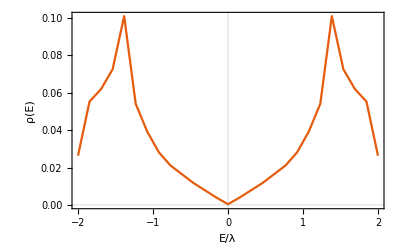

0.564441

-Graphics3D-

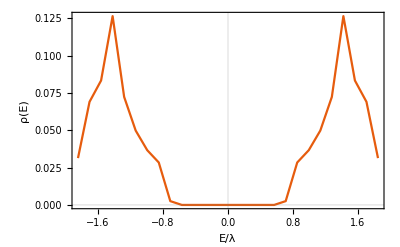

0.606598

-Graphics3D-

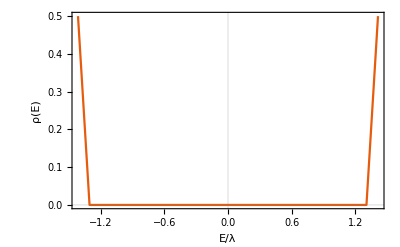

```mathematica
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];

Clear[orderedGaugedEigensystem]
orderedGaugedEigensystem[M_,f_:Re]:=Module[{vals,vecs, order,phase},
{vals,vecs} = Eigensystem[M];
order = Ordering[f[vals]];
vals=vals[[order]];
vecs=vecs[[order]];
phase = AbsArg[vecs[[1,1]]][[2]];
If[phase≠Mod[phase,π/2],vecs*=ⅈ];
vecs=vecsᵀ;
{vals,vecs}
];

(* compute density of states *)
Clear[DOS]
DOS[E_,NE_]:=Module[{min,max,Eints,dos},
{min,max}=MinMax[E];
Eints =min+ Table[(max-min)/NE n,{n,0,NE}];
dos=Table[Length[Nearest[E,e,{Infinity,(max-min)/(2*NE)}]],{e,Eints}];
(*Print[Eints,Length[E]];*)
{Eints,dos/Length[E]}ᵀ
];

(* convenient matrices to define the BBH model *)
Clear[λ,γ,Δ,L,ks,kxs,kys,tp,bands, Γ,h,spec,spec2,ϵ,ϵ2]
Γ[0]=PauliMatrix[3]⊗PauliMatrix[0]//ArrayFlatten;
Table[Γ[k]=PauliMatrix[2]⊗PauliMatrix[k]//ArrayFlatten,{k,1,3}];
Γ[4]=PauliMatrix[1]⊗PauliMatrix[0]//ArrayFlatten;

(* BBH hamiltonian, spectrum & modes *)
h[kx_,ky_,γ_,λ_,Δ_,ϕ_]:=(γ+λ Cos[kx])Γ[4]+λ Cos[kx+ϕ]Γ[3]+(γ+λ Cos[ky])Γ[2]+λ Cos[ky+ϕ]Γ[1]+Δ Γ[0];
ϵ[kx_,ky_,γ_,λ_,Δ_,ϕ_]:=orderedEigensystem[N[h[kx,ky,γ,λ,Δ,ϕ]]];
spec[γ_,λ_,Δ_,ϕ_,kx_,ky_]:={kx,ky,ϵ[kx,ky,γ,λ,Δ,ϕ]}

ϵ2[kx_,ky_,γ_,λ_,Δ_,ϕ_]:=orderedGaugedEigensystem[N[h[kx,ky,γ,λ,Δ,ϕ]]];
spec2[γ_,λ_,Δ_,ϕ_,kx_,ky_]:={kx,ky,ϵ2[kx,ky,γ,λ,Δ,ϕ]}

Lx=Ly=100;(* momentum space discretization *)
NE=If[OddQ[Lx/4],Lx/4+1,Lx/4]; (* discretization of the DOS *)
kxs = Table[N[(2π)/Lx n-π],{n,0,Lx}];
kys = Table[N[(2π)/Ly n]-π,{n,0,Ly}];

(* ϕ = 0, bulk gap closing *)
AbsoluteTiming[res =Table[spec[0.,1,0.0,0 π/4,kx,ky],{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]

(* ϕ = π/4, bulk gap is finite *)
AbsoluteTiming[res =Table[spec[0.,1,0.0,π/4,kx,ky],{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]

(* ϕ = π/2, bulk gap maximal *)
AbsoluteTiming[res =Table[spec[0.,1,0.0,π/2,kx,ky],{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]
```

0.092305

-Graphics3D-

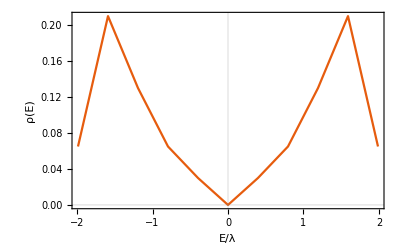

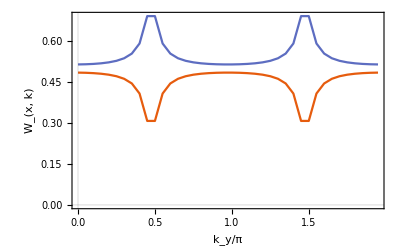

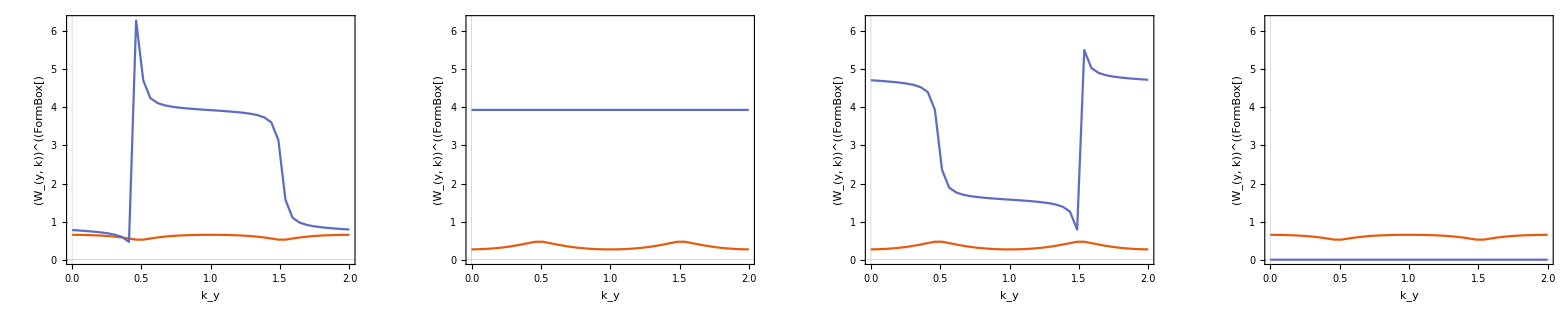

{0.5,0.5}

```mathematica
Lx=Ly=40;(* momentum space discretization *)
NE=If[OddQ[Lx/4],Lx/4+1,Lx/4]; (* discretization of the DOS *)
kxs = Table[N[(2π)/Lx n],{n,0,Lx-1}];
kys = Table[N[(2π)/Ly n],{n,0,Ly-1}];

AbsoluteTiming[res =Table[spec[0.0,1,0.,0.1π/2,kx,ky],{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]

Clear[Fk,Norb,x,y,Fx,u,ux,Fx]
Norb=2;
Wtilde={};
Wx = ConstantArray[0,{Lx,Ly,2,2}];
Do[
Wxy={};
Vxy={};
Axy={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[Mod[x+xp-1,Lx]+1,y,3,2,;;,;;Norb]];
ux=res[[Mod[x+xp,Lx]+1,y,3,2,;;,;;Norb]];
prod = ux†.u;
Fxy=prod.Fxy;
Fxy/=Norm[Fxy]; (* this might stabilize *)
,{x,1,Length[res]}];
{vals,vecs} = orderedEigensystem[Fxy,Im];
AppendTo[Wxy,Table[Mod[(AbsArg[e][[2]])/(2π)+0.5,1],{e,vals}]];
AppendTo[Axy,Table[AbsArg[e][[1]],{e,vals}]];
vs=res[[Mod[xp,Lx]+1,y,3,2,;;,;;Norb]].vecs;
AppendTo[Vxy,vs];
Wx[[xp+1,y]]=prod;
,{y,1,Length[res[[1]]]}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Ly]+1]]†.Vxy[[n]],{n,Ly}]]]];
,{xp,0,Lx-1}]
ListPlot[Wxyᵀ,PlotRange->Full,Joined->True,PlotTheme->"Scientific",DataRange->MinMax[kys]/π,FrameLabel->{"k_y/π","W_(x, k)"}]
GraphicsRow[Table[ListPlot[Mod[AbsArg[Vxy[[;;,n]]][[;;,2]]ᵀ,2π],PlotRange->{{0,2},{0,2π}},Joined->True,DataRange->{0,2},PlotTheme->"Scientific",FrameLabel->{"k_y",StringForm["(W_(y, k))^(`1`)",n]}],{n,4}],ImageSize->2000]
py=Mean[Mod[Im[Log[Wtilde]],2π]]/(2π) (* polarization == 0.0, if |γ| > |λ| (triv. phase) *)
```

```mathematica
mx = ArrayFlatten[PauliMatrix[1]⊗PauliMatrix[3]];
my = ArrayFlatten[PauliMatrix[1]⊗PauliMatrix[1]];
```

```mathematica
h[kx,ky,γ,λ,0,ϕ]//MatrixForm
```

(0 | 0 | γ+λ Cos[kx]-ⅈ λ Cos[kx+ϕ] | -γ-λ Cos[ky]-ⅈ λ Cos[ky+ϕ]
0 | 0 | γ+λ Cos[ky]-ⅈ λ Cos[ky+ϕ] | γ+λ Cos[kx]+ⅈ λ Cos[kx+ϕ]
γ+λ Cos[kx]+ⅈ λ Cos[kx+ϕ] | γ+λ Cos[ky]+ⅈ λ Cos[ky+ϕ] | 0 | 0
-γ-λ Cos[ky]+ⅈ λ Cos[ky+ϕ] | γ+λ Cos[kx]-ⅈ λ Cos[kx+ϕ] | 0 | 0)

```mathematica
v[kx_,ky_,γ_,λ_,ϕ_]=h[kx,ky,γ,λ,0,ϕ][[1;;2,3;;4]]//FullSimplify
%//MatrixForm
h[kx,ky,0,1,0,π/2]//FullSimplify//MatrixForm
v[kx,ky,0,1,π/2]//FullSimplify//MatrixForm
```

{{γ+λ Cos[kx]-ⅈ λ Cos[kx+ϕ],-γ-λ (Cos[ky]+ⅈ Cos[ky+ϕ])},{γ+λ Cos[ky]-ⅈ λ Cos[ky+ϕ],γ+λ Cos[kx]+ⅈ λ Cos[kx+ϕ]}}

(γ+λ Cos[kx]-ⅈ λ Cos[kx+ϕ] | -γ-λ (Cos[ky]+ⅈ Cos[ky+ϕ])
γ+λ Cos[ky]-ⅈ λ Cos[ky+ϕ] | γ+λ Cos[kx]+ⅈ λ Cos[kx+ϕ])

(0 | 0 | ⅇ^(ⅈ kx) | -ⅇ^(-ⅈ ky)
0 | 0 | ⅇ^(ⅈ ky) | ⅇ^(-ⅈ kx)
ⅇ^(-ⅈ kx) | ⅇ^(-ⅈ ky) | 0 | 0
-ⅇ^(ⅈ ky) | ⅇ^(ⅈ kx) | 0 | 0)

(ⅇ^(ⅈ kx) | -ⅇ^(-ⅈ ky)
ⅇ^(ⅈ ky) | ⅇ^(-ⅈ kx))

```mathematica
{vals,vecs}=orderedEigensystem[h[kx,ky,γ,λ,0,π/2]];
```

```mathematica
vals//FullSimplify
```

{-√2 √(γ^2+λ^2+γ λ (Cos[kx]+Cos[ky])),-√2 √(γ^2+λ^2+γ λ (Cos[kx]+Cos[ky])),√2 √(γ^2+λ^2+γ λ (Cos[kx]+Cos[ky])),√2 √(γ^2+λ^2+γ λ (Cos[kx]+Cos[ky]))}

```mathematica
Det[v[kx,ky,0,λ]]//FullSimplify
```

λ^2 (Cos[kx]^2+Cos[ky]^2+Cos[kx+ϕ]^2+Cos[ky+ϕ]^2)

```mathematica
vecs[[;;,1]]/.{ϕ->π/2}//FullSimplify
```

{ⅇ^(-ⅈ ky)/(√2),-ⅇ^(-ⅈ kx)/(√2),0,1}

```mathematica
Γ[0].h[kx,ky,γ,λ,Δ,ϕ]+h[kx,ky,γ,λ,Δ,ϕ].Γ[0]//MatrixForm
Γ[0]//MatrixForm
```

(2 Δ | 0 | 0 | 0
0 | 2 Δ | 0 | 0
0 | 0 | 2 Δ | 0
0 | 0 | 0 | 2 Δ)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
v[kx,ky,γ,λ]ᵀ.v[kx,ky,γ,λ]//ExpandAll//FullSimplify
%//MatrixForm
```

{{((1-ⅈ) γ+λ Cos[kx]-λ (ⅈ (Cos[ky]-Cos[kx+ϕ])+Cos[ky+ϕ])) ((1+ⅈ) γ+λ (Cos[kx]+ⅈ (Cos[ky]+Cos[kx+ϕ])+Cos[ky+ϕ])),2 ⅈ λ ((γ+λ Cos[ky]) Cos[kx+ϕ]+(γ+λ Cos[kx]) Cos[ky+ϕ])},{2 ⅈ λ ((γ+λ Cos[ky]) Cos[kx+ϕ]+(γ+λ Cos[kx]) Cos[ky+ϕ]),((1-ⅈ) γ+λ (-ⅈ Cos[kx]+Cos[ky]-Cos[kx+ϕ]+ⅈ Cos[ky+ϕ])) ((1+ⅈ) γ+λ (ⅈ Cos[kx]+Cos[ky]+Cos[kx+ϕ]+ⅈ Cos[ky+ϕ]))}}

(((1-ⅈ) γ+λ Cos[kx]-λ (ⅈ (Cos[ky]-Cos[kx+ϕ])+Cos[ky+ϕ])) ((1+ⅈ) γ+λ (Cos[kx]+ⅈ (Cos[ky]+Cos[kx+ϕ])+Cos[ky+ϕ])) | 2 ⅈ λ ((γ+λ Cos[ky]) Cos[kx+ϕ]+(γ+λ Cos[kx]) Cos[ky+ϕ])
2 ⅈ λ ((γ+λ Cos[ky]) Cos[kx+ϕ]+(γ+λ Cos[kx]) Cos[ky+ϕ]) | ((1-ⅈ) γ+λ (-ⅈ Cos[kx]+Cos[ky]-Cos[kx+ϕ]+ⅈ Cos[ky+ϕ])) ((1+ⅈ) γ+λ (ⅈ Cos[kx]+Cos[ky]+Cos[kx+ϕ]+ⅈ Cos[ky+ϕ])))

```mathematica
ArrayFlatten[Inverse[v[kx,ky,γ,λ]].D[v[kx,ky,γ,λ],kx]/.{ϕ->π/2}//FullSimplify]
%//MatrixForm
```

{{-(ⅈ λ (ⅇ^(-ⅈ kx) γ+λ))/(2 (γ^2+λ^2+γ λ (Cos[kx]+Cos[ky]))),(λ (γ+ⅇ^(-ⅈ ky) λ) (-ⅈ Cos[kx]+Sin[kx]))/(2 (γ^2+λ^2+γ λ (Cos[kx]+Cos[ky])))},{-(ⅈ ⅇ^(-ⅈ kx) λ (γ+ⅇ^(ⅈ ky) λ))/(2 (γ^2+λ^2+γ λ (Cos[kx]+Cos[ky]))),(ⅈ λ (ⅇ^(ⅈ kx) γ+λ))/(2 (γ^2+λ^2+γ λ (Cos[kx]+Cos[ky])))}}

(-(ⅈ λ (ⅇ^(-ⅈ kx) γ+λ))/(2 (γ^2+λ^2+γ λ (Cos[kx]+Cos[ky]))) | (λ (γ+ⅇ^(-ⅈ ky) λ) (-ⅈ Cos[kx]+Sin[kx]))/(2 (γ^2+λ^2+γ λ (Cos[kx]+Cos[ky])))
-(ⅈ ⅇ^(-ⅈ kx) λ (γ+ⅇ^(ⅈ ky) λ))/(2 (γ^2+λ^2+γ λ (Cos[kx]+Cos[ky]))) | (ⅈ λ (ⅇ^(ⅈ kx) γ+λ))/(2 (γ^2+λ^2+γ λ (Cos[kx]+Cos[ky]))))

```mathematica
(* double FT *)
Lx=Ly=8;
Clear[δ,Hrs,γ,λ,Δ];
(h[kx,ky,γ,λ,Δ,ϕ]*Exp[ⅈ*{kx,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2]*δ[y1,y2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2+1]*δ[y1,y2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1+1,x2]*δ[y1,y2],ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1,y2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1+1,y2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2-ⅈ ϕ)-> ⅇ^(-ⅈ ϕ)δ[x1,x2+1]δ[y1,y2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2+ⅈ ϕ)-> ⅇ^(+ⅈ ϕ)δ[x1+1,x2]δ[y1,y2], ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2-ⅈ ϕ)-> ⅇ^(-ⅈ ϕ)δ[x1,x2]δ[y1,y2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2+ⅈ ϕ)->ⅇ^(+ⅈ ϕ)δ[x1,x2]δ[y1+1,y2],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2-ⅈ ϕ)->ⅇ^(-ⅈ ϕ)δ[x1,x2]δ[y1+1,y2],ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2+ⅈ ϕ)->ⅇ^(+ⅈ ϕ)δ[x1,x2]δ[y1,y2+1]};
(* assign local real space Hamiltonian *)
Hrs[x1_,x2_,y1_,y2_]=%;
δ[x_,y_]=If[x==y,1,0];
(* now construct the full one *)
Clear[Hfull];
pbc=False;
Hfull= ConstantArray[0,{Lx,Ly,Length[Hrs[1,1,1,1]],Lx,Ly,Length[Hrs[1,1,1,1]]}];
Do[
If[x1>0&&x1≤Lx&&y2>0&&y2≤Ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

(* the boundary terms *)
If[x1==Lx+1&&y2>0&&y2≤Ly&&pbc,
Hfull[[1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==Ly+1&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,1,;;]]+=Hrs[x1,x2,y1,y2];
];

If[x1==0&&y2>0&&y2≤Ly&&pbc,
Hfull[[Lx,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==0&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,Ly,;;]]+=Hrs[x1,x2,y1,y2];
];
,{x1,x2-2,x2+2},{x2,Lx},{y1,Ly},{y2,y1-1,y1+1}];
Hmat=ArrayReshape[Hfull,{Lx*Ly*4,Lx*Ly*4}];

L=Lx;(* momentum space discretization *)
ks = Table[N[(2π)/L n-π],{n,0,L}];
γs=Range[-2,2,0.1];
phi=0.5π;
bands={};
modes={};
bandsPBC={};
Monitor[
Do[
res = orderedEigensystem[N[(Hmat/.{γ->g,λ->1.0,Δ->0.0,ϕ->phi})]];
AppendTo[bands,res[[1]]];
AppendTo[modes,res[[2]]];
res =Table[spec[g,1.,0.,phi,kxs,kys],{kxs,ks},{kys,ks}];
AppendTo[bandsPBC,Flatten[res[[;;,;;,3,1]]]];
,{g,γs}]
,g]
(* first plot PBC bands *)
plotPBC=ListPlot[Re[bandsPBC]ᵀ,DataRange->MinMax[γs],Joined->True,FrameLabel->{"γ","E/λ"},PlotTheme->"Scientific"]
(* compare with OBC bands *)
Show[ListPlot[bandsᵀ,DataRange->MinMax[γs],Joined->True,FrameLabel->{"γ","E/λ"},PlotTheme->"Scientific"]]

(* plot modes *)
modesReshaped=Table[ArrayReshape[modes[[i,;;,j]],{Lx,Ly,4}],{i,Length[modes]},{j,Length[modes[[1,1]]]}];
Manipulate[GraphicsRow[Table[ListPlot3D[Flatten[Table[{lx,ly,Abs[modesReshaped[[i,j,lx,ly,b]]]},{lx,Lx},{ly,Ly}],1],PlotRange->Full,Mesh->None,PlotTheme->"Scientific",AxesLabel->{"x","y",StringForm["(ψ_(`1`))^*ψ_(`1`)",b]}],{b,1,Length[modesReshaped[[i,j,1,1]]]}]],{{i,Floor[Length[modesReshaped]/2]},1,Length[modesReshaped],1},{{j,Floor[Length[modesReshaped[[1]]]/2]},1,Length[modesReshaped[[1]]],1}]
```

```mathematica
(* x-direction finite, periodic along y *)
Clear[δ,Hmixed,γ,λ,Δ];
γs=Range[-2,2,0.1];
(h[kx,ky,γ,λ,Δ,phi]*Exp[ⅈ*{kx,0}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ kx x1-ⅈ kx x2)->δ[x1,x2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2) -> δ[x1,x2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2)->δ[x1,x2] ⅇ^(ⅈ ky),ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2)->ⅇ^(-ⅈ ky)δ[x1,x2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2)->δ[x1+1,x2]};
(* assign local real space Hamiltonian *)
Hmixed[x1_,x2_,ky_]=%;
δ[x_,y_]=If[x==y,1,0];
(* now construct the full one *)
Clear[Hfull];
pbc=False;
Hfull= ConstantArray[0,{Lx,Length[Hmixed[1,1,1]],Lx,Length[Hmixed[1,1,1]]}];
Do[
If[x1>0&&x1≤Lx,
Hfull[[x1,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];

(* the boundary terms *)
If[x1==Lx+1&&pbc,
Hfull[[1,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];

If[x1==0&&pbc,
Hfull[[Lx,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];
,{x1,x2-2,x2+2},{x2,Lx}];
Hmat=ArrayReshape[Hfull,{Lx*4,Lx*4}];
ks = Table[N[(2π)/Ly n-π],{n,0,Ly}];
ListPlot[Table[Sort[Eigenvalues[Hmat/.{ky->k,γ->0.,λ->1,Δ->0.}]],{k,ks}]ᵀ,DataRange->MinMax[ks]/π,Joined->True,PlotTheme->"Scientific",FrameLabel->{"k_y","E/λ"}]
```

```mathematica
(* y-direction finite, periodic along x *)
Clear[δ,Hmixed,γ,λ,Δ];
γs=Range[-2,2,0.1];
(h[kx,ky,γ,λ,Δ,phi]*Exp[ⅈ*{0,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ ky y1-ⅈ ky y2)->δ[y1,y2],ⅇ^(-ⅈ kx+ⅈ ky y1-ⅈ ky y2) -> ⅇ^(-ⅈ kx)δ[y1,y2],ⅇ^(ⅈ ky+ⅈ ky y1-ⅈ ky y2)->δ[y1+1,y2],ⅇ^(-ⅈ ky+ⅈ ky y1-ⅈ ky y2)->δ[y1,y2+1],ⅇ^(ⅈ kx+ⅈ ky y1-ⅈ ky y2)->ⅇ^(ⅈ kx)δ[y1,y2]};
(* assign local real space Hamiltonian *)
Hmixed[y1_,y2_,kx_]=%;
δ[x_,y_]=If[x==y,1,0];
(* now construct the full one *)
Clear[Hfull];
pbc=False;
Hfull= ConstantArray[0,{Lx,Length[Hmixed[1,1,1,1]],Lx,Length[Hmixed[1,1,1,1]]}];
Do[
If[y2>0&&y2≤Ly,
Hfull[[y1,;;,y2,;;]]+=Hmixed[y1,y2,kx];
];

(* the boundary terms *)
If[y2==Ly+1&&pbc,
Hfull[[y1,;;,1,;;]]+=Hmixed[y1,y2,kx];
];
If[y2==0&&pbc,
Hfull[[y1,;;,Ly,;;]]+=Hmixed[y1,y2,kx];
];
,{y1,Ly},{y2,y1-1,y1+1}];
Hmat=ArrayReshape[Hfull,{Ly*4,Ly*4}];
ks = Table[N[(2π)/Lx n-π],{n,0,Lx}];
res = Table[orderedEigensystem[Hmat/.{kx->k,γ->0.,λ->1,Δ->0.}],{k,ks}];
ListPlot[res[[;;,1]]ᵀ,DataRange->MinMax[ks]/π,Joined->True,PlotTheme->"Scientific",FrameLabel->{"k_x","E/λ"}]
```

```mathematica
modesReshaped=Table[ArrayReshape[res[[i,2,;;,j]],{Lx,4}],{i,Length[res]},{j,Length[res[[1,2,1]]]}];
Manipulate[GraphicsRow[Table[ListPlot[Table[{lx,Abs[modesReshaped[[i,j,lx,b]]]},{lx,Lx}],PlotRange->Full,Mesh->None,PlotTheme->"Scientific",Joined->True,FrameLabel->{"x",StringForm["ψ_(`1`)(k_(`2`))^*ψ_(`1`)(k_(`2`))",b,i]}],{b,1,Length[modesReshaped[[i,1,1]]]}]],{{i,Floor[Length[modesReshaped]/2]},1,Length[modesReshaped],1},{{j,Floor[Length[modesReshaped[[1]]]/2]},1,Length[modesReshaped[[1]]],1}]
```

```mathematica
Clear[h,Δ,kx,ky,H,Δuu,Δud,Δdu,Δdd]
ξ[kx_,ky_]=(1-Cos[kx]-Cos[ky]);
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+
{bx,by,bz}.Table[PauliMatrix[i],{i,3}];
h2[kx_,ky_]=-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3];


Δuu[kx_,ky_]=+(Sin[kx]-ⅈ Sin[ky]);
Δdd[kx_,ky_]=+(Sin[kx]+ⅈ Sin[ky]);
Δud[kx_,ky_]=-(sx*Cos[kx]+sy*Cos[ky]);
Δdu[kx_,ky_]=+(sx*Cos[kx]+sy*Cos[ky]);
Δ[kx_,ky_]={{Δuu[kx,ky],-Δud[kx,ky]},{Δdu[kx,ky],-Δdd[kx,ky]}};

Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],Δ[kx,ky]},{Δ[kx,ky]*,h2[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}];

(* check if hermitian *)
Print["H is hermitian: "<>ToString[DeleteDuplicates[Flatten[Refine[H[kx,ky]-H[kx,ky]†,{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}]]]=={0}]]
```

H is hermitian: True

```mathematica
H[kx,ky]/.{bz->0,bx->-.3,by->0.,sx->0,sy->.3}
```

{{1-Cos[kx]-Cos[ky],-0.3+0. ⅈ,Sin[kx]-ⅈ Sin[ky],0.3 Cos[ky]},{-0.3+0. ⅈ,1-Cos[kx]-Cos[ky],0.3 Cos[ky],-Sin[kx]-ⅈ Sin[ky]},{Sin[kx]+ⅈ Sin[ky],0.3 Cos[ky],-1+Cos[kx]+Cos[ky],-0.3+0. ⅈ},{0.3 Cos[ky],-Sin[kx]+ⅈ Sin[ky],-0.3+0. ⅈ,-1+Cos[kx]+Cos[ky]}}

0.036038

0.038176

-Graphics3D-

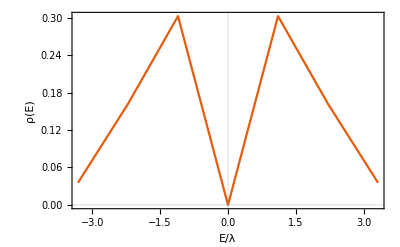

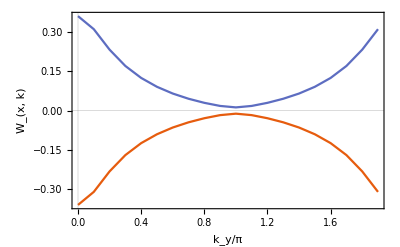

{0.500095,0.500095}

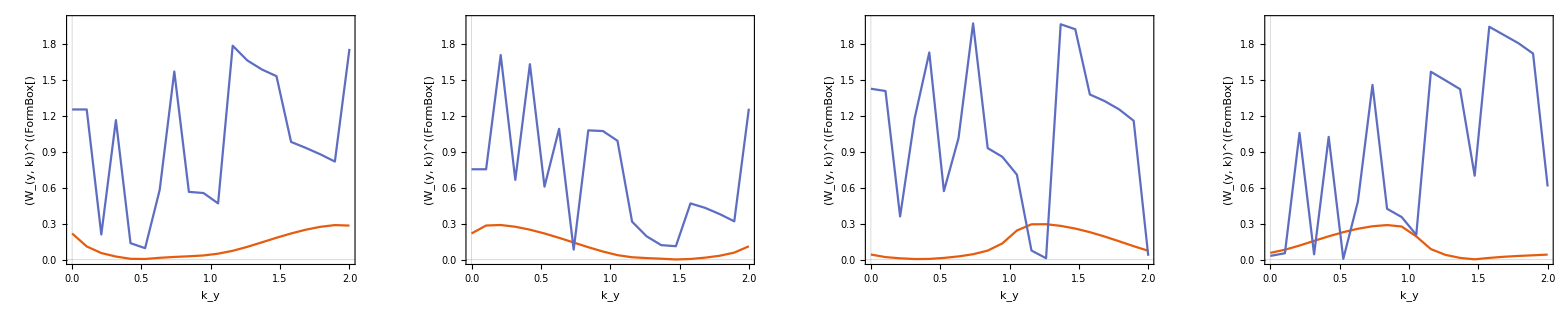

```mathematica
Clear[orderedGaugedEigensystem]
orderedGaugedEigensystem[M_,f_:Re]:=Module[{vals,vecs, order,phase},
{vals,vecs} = Eigensystem[M];
order = Ordering[f[vals]];
vals=vals[[order]];
vecs=vecs[[order]];
phase = AbsArg[vecs[[1,1]]][[2]];
If[phase≠Mod[phase,π/2],vecs/=Exp[ⅈ*(phase-Mod[phase,π/2])]];
vecs=vecsᵀ;
{vals,vecs}
];
Clear[regauge]
regauge[M_]:=Module[{vecs,phase},
vecs = M;
phase = AbsArg[vecs[[1,1]]][[2]];
If[phase≠Mod[phase,2π],vecs/=Exp[ⅈ*(phase-Mod[phase,2π])]];
vecs
];
Lx=Ly=20;(* momentum space discretization *)
NE=If[OddQ[Lx/4],Lx/4+1,Lx/4]; (* discretization of the DOS *)
kxs = Table[N[(2π)/Lx n],{n,0,Lx-1}];
kys = Table[N[(2π)/Ly n],{n,0,Ly-1}];

AbsoluteTiming[res =Table[{kx,ky,orderedGaugedEigensystem[H[kx,ky]/.{bz->0.,bx->-0.3,by->0.,sx->-0.,sy->0.3}]},{kx,kxs},{ky,kys}];][[1]]
AbsoluteTiming[res =Table[{kx,ky,orderedGaugedEigensystem[H[kx,ky]/.{bz->0.,bx->0.3,by->-0.,sx->0.,sy->0.3}]},{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]

Clear[Fk,Norb,x,y,Fx,u,ux,Fx]
Norb=2;
Wtilde={};
Wx = ConstantArray[0,{Lx,Ly,2,2}];
Do[
Wxy={};
Vxy={};
Axy={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[Mod[x+xp-1,Lx]+1,y,3,2,;;,;;Norb]];
ux=res[[Mod[x+xp,Lx]+1,y,3,2,;;,;;Norb]];
prod = ux†.u;
Fxy=prod.Fxy;
Fxy/=Norm[Fxy]; (* this might stabilize *)
,{x,1,Length[res]}];
{vals,vecs} = orderedEigensystem[Fxy,Im];
AppendTo[Wxy,Table[(AbsArg[e][[2]])/(2π),{e,vals}]];
AppendTo[Axy,Table[AbsArg[e][[1]],{e,vals}]];
vs=res[[Mod[xp,Lx]+1,y,3,2,;;,;;Norb]].vecs;
AppendTo[Vxy,vs];
Wx[[xp+1,y]]=prod;
,{y,1,Length[res[[1]]]}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Ly]+1]]†.Vxy[[n]],{n,Ly}]]]];
,{xp,0,Lx-1}]
ListPlot[Wxyᵀ,PlotRange->Full,Joined->True,PlotTheme->"Scientific",DataRange->MinMax[kys]/π,FrameLabel->{"k_y/π","W_(x, k)"}]
py=Mean[Mod[Im[Log[Wtilde]],2π]]/(2π) (* polarization == 0.0, if |γ| > |λ| (triv. phase) *)
GraphicsRow[Table[ListPlot[Mod[AbsArg[Vxy[[;;,n]]][[;;,2]]ᵀ,2π]/π,PlotRange->{{0,2},{0,2}},Joined->True,DataRange->{0,2},PlotTheme->"Scientific",FrameLabel->{"k_y",StringForm["(W_(y, k))^(`1`)",n]}],{n,4}],ImageSize->2000]
```